## Self-Normalizing Neural Networks

This is an improved kind of FNN - the SNN. Describe Network and describe properties.
The entering input into SNN require explicit normalization, but after that the characteristics of the network provide that the neuron activations converge towards zero mean and unit variance. The activations which induce self-normalizing propeties are the SELUs-scaled exponential linear units. with Banach fixed-point theorem it is proved that activations converge towards zero mean and unit variance even with presence of noise and perturbations. This is why SNN are highly robust, have strong regularization schemes. Even ifthe activations are not clos to unit variance it is proved an upper and lower bound on variance, so vanishing and exploding gradients are impossible. We used SNNs to classify diseases by some given atributes. The classified diseases were in the field of dermatology, breast cancer, kidney and Parkinson. The SNN classified it perfectly, over 90% accuracy, some even had a 100% of accuracy. Winning SNN architectures are offten very deep. 
Theorem 4 (Banach Fixed Point Theorem). Let (X, d) be a non-empty complete metric space with a
contraction mapping f : X → X. Then f has a unique fixed-point xf ∈ X with f(xf ) = xf . Every
sequence xn = f (xn−1 ) with starting element x0 ∈ X converges to the fixed point: xn −−−→ xf .


What exactly is a SNN? Definition 1 (Self-normalizing neural net). A neural network is self-normalizing if it possesses a mapping g : Ω  → Ω for each activation y that maps mean and variance from one layer to the next and has a stable and attracting fixed point depending on (ω, τ ) in Ω. Furthermore, the mean and the variance remain in the domain Ω, that is g(Ω) ⊆ Ω, where Ω = {(μ, ν) | μ ∈ [μmin, μmax], ν ∈ [νmin, νmax]}. When iteratively applying the mapping g, each point within Ω converges to this fixed point.

```mathematica
SNNnetClassification[dropoutrate_,nhidden_,nlayers_,decoder_]:=NetChain[Join[Flatten@Table[{LinearLayer[nhidden],ElementwiseLayer["SELU"],DropoutLayer[dropoutrate,"Method"->"AlphaDropout"]},nlayers-1],{LinearLayer[],SoftmaxLayer[]}],"Output"->decoder];
```

```mathematica
FNNnetClassification[best_,decoder_]:=NetChain[Join[Flatten@Table[{LinearLayer[best⟦2⟧],ElementwiseLayer["ReLU"],DropoutLayer[best⟦1⟧]},best⟦3⟧-1],{LinearLayer[],SoftmaxLayer[]}],"Output"->decoder];
```

```mathematica
SNNnetClassification[0.1,8,4,dermadec]
```

NetChain[<>]

## Motivation

The differential diagnosis of Erythemato-Squamous diseases is a real
problem in dermatology.They all share the clinical features of
erythema and scaling, with very little differences. Usually a biopsy is necessary for the diagnosis but unfortunately these diseases share many histopathological features as well. Another difficulty for the differential diagnosis is that a disease may show the features of another disease at the beginning stage and may have the characteristic features at the following stages. With the data set taken from UCI we train neural networks and observe their efficiency to determine the disease.

## Dermatology

### Overview

```mathematica
Dataset[{}]
```

Dataset[<>]

### Classes

```mathematica
Dataset[{}]
```

Dataset[<>]

### Attributes

```mathematica
attributes=Dataset[{}]
```

Dataset[<>]

```mathematica
Import["https://archive.ics.uci.edu/ml/machine-learning-databases/dermatology/dermatology.names","Text"]
```

1. Title: Dermatology Database

2. Source Information:
   (a) Original owners:
       -- 1. Nilsel Ilter, M.D., Ph.D., 
             Gazi University, 
             School of Medicine
             06510 Ankara, Turkey
             Phone: +90 (312) 214 1080

       -- 2. H. Altay Guvenir, PhD., 
             Bilkent University,
             Department of Computer Engineering and Information Science,
             06533 Ankara, Turkey
             Phone: +90 (312) 266 4133
             Email: guvenir@cs.bilkent.edu.tr

   (b) Donor: H. Altay Guvenir,
              Bilkent University,
              Department of Computer Engineering and Information Science,
              06533 Ankara, Turkey
              Phone: +90 (312) 266 4133
              Email: guvenir@cs.bilkent.edu.tr

   (c) Date:  January, 1998

3. Past Usage:
   1. G. Demiroz, H. A. Govenir, and N. Ilter, 
      "Learning Differential Diagnosis of Eryhemato-Squamous Diseases using
       Voting Feature Intervals", Aritificial Intelligence in Medicine,

      The aim is to determine the type of Eryhemato-Squamous Disease.

4. Relevant Information:
     This database contains 34 attributes, 33 of which are linear
     valued and one of them is nominal. 

     The differential diagnosis of erythemato-squamous diseases is a real
     problem in dermatology. They all share the clinical features of
     erythema and scaling, with very little differences. The diseases in
     this group are psoriasis, seboreic dermatitis, lichen planus, 
     pityriasis rosea, cronic dermatitis, and pityriasis rubra pilaris.
     Usually a biopsy is necessary for the diagnosis but unfortunately
     these diseases share many histopathological features as
     well. Another difficulty for the differential diagnosis is that a
     disease may show the features of another disease at the beginning
     stage and may have the characteristic features at the following stages. 
     Patients were first evaluated clinically with 12 features.
     Afterwards, skin samples were taken for the evaluation of 22
     histopathological features. The values of the histopathological features
     are determined by an analysis of the samples under a microscope. 

     In the dataset constructed for this domain, the family history feature
     has the value 1 if any of these diseases has been observed in the
     family, and 0 otherwise. The age feature simply represents the age of
     the patient. Every other feature (clinical and histopathological) was
     given a degree in the range of 0 to 3. Here, 0 indicates that the
     feature was not present, 3 indicates the largest amount possible,
     and 1, 2 indicate the relative intermediate values.

     The names and id numbers of the patients were recently 
     removed from the database.

5. Number of Instances: 366

6. Number of Attributes: 34

7. Attribute Information:
   -- Complete attribute documentation:
      Clinical Attributes: (take values 0, 1, 2, 3, unless otherwise indicated)
      1: erythema
      2: scaling
      3: definite borders
      4: itching
      5: koebner phenomenon
      6: polygonal papules
      7: follicular papules
      8: oral mucosal involvement
      9: knee and elbow involvement
     10: scalp involvement
     11: family history, (0 or 1)
     34: Age (linear)

     Histopathological Attributes: (take values 0, 1, 2, 3)
     12: melanin incontinence
     13: eosinophils in the infiltrate
     14: PNL infiltrate
     15: fibrosis of the papillary dermis
     16: exocytosis
     17: acanthosis
     18: hyperkeratosis
     19: parakeratosis
     20: clubbing of the rete ridges
     21: elongation of the rete ridges
     22: thinning of the suprapapillary epidermis
     23: spongiform pustule
     24: munro microabcess
     25: focal hypergranulosis
     26: disappearance of the granular layer
     27: vacuolisation and damage of basal layer
     28: spongiosis
     29: saw-tooth appearance of retes
     30: follicular horn plug
     31: perifollicular parakeratosis
     32: inflammatory monoluclear inflitrate
     33: band-like infiltrate
      
8. Missing Attribute Values: 8 (in Age attribute). Distinguished with '?'.

9. Class Distribution:
       Database:  Dermatology
       
       Class code:   Class:                  Number of instances:
       1             psoriasis			    112
       2             seboreic dermatitis             61
       3             lichen planus                   72
       4             pityriasis rosea                49
       5             cronic dermatitis               52    
       6             pityriasis rubra pilaris        20

Importing the dermatology set from UCI Machine Learning repository.  Preprocessing and creation of the train and test sets (for FNN and the ClassifierFunction[]) and the normalized train and test sets (for the SNN)

```mathematica
link="https://archive.ics.uci.edu/ml/machine-learning-databases/dermatology/dermatology.data";
dermaDatawMissing =ReplaceAll[Import[link, "CSV"], "?"->Missing[]];

dermaData=DeleteMissing[dermaDatawMissing,1,2];
dermaDatawRule=Table[Drop[dermaData⟦i⟧,-1]->Last@dermaData⟦i⟧,{i,1,Length@dermaData}];

{dermatrain,dermatest}={RandomSample[dermaDatawRule,Round[0.9Length@dermaDatawRule]],Complement[dermaDatawRule,dermatrain]};

dermaext=FeatureExtraction[N@Keys@dermaDatawRule,"StandardizedVector"];

{dermatrainSNN,dermatestSNN}={dermaext[Keys@dermatrain]->Values[dermatrain],dermaext[Keys@dermatest]->Values[dermatest]};

dermatestSNN=Table[dermatestSNN[[1,i]]->dermatestSNN[[2,i]],{i,1,Length@dermatestSNN⟦1⟧}];
```

Self-normalizing Neural Network and its training, together with their Classifier Measurement functions.  48 of SNN are created, with different hyperparameters for each to find the best fit:

```mathematica
dermadec=NetDecoder[{"Class",Range[6]}];

dermaLoss=CrossEntropyLossLayer["Index","Target"->NetEncoder[{"Class",{1,2,3,4,5,6}}]];

dermaNet=<|Flatten@Table[{i,j,k}->SNNnetClassification[i,j,k,dermadec],{i,{0.01,0.05,0.1}},{j,{32,64,128,256}},{k,{4,8,16,32}}]|>;

trainedNet=<|Table[SeedRandom[8];key->NetTrain[dermaNet[key],dermatrainSNN,LossFunction->dermaLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]],{key,Keys@dermaNet}]|>;

dermacm=<|Table[key->ClassifierMeasurements[trainedNet[key],dermatestSNN],{key,Keys@trainedNet}]|>;

dermaAccuracy=<|Table[key->dermacm[key]["Accuracy"],{key,Keys@trainedNet}]|>;
```

The accuracies of all the 48 SNNs plotted in a ListPlot[]:

```mathematica
Sort[Values@dermaAccuracy]
```

{0.222222,0.333333,0.444444,0.5,0.611111,0.722222,0.722222,0.805556,0.888889,0.916667,0.916667,0.944444,0.944444,0.944444,0.944444,0.944444,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,0.972222,1.,1.,1.,1.,1.,1.,1.}

```mathematica
dermaListPlot=ListPlot[dermaAccuracy,PlotTheme->"Detailed",FrameLabel->{"Neural Net","Accuracy"},PlotLabel->Style["Dermatology data",18,Black]]
```

The hyperparameters of  the best (or one of the best)  SNN:

```mathematica
best=Last@Keys@dermaAccuracy⟦Ordering[Values@dermaAccuracy]⟧
```

{0.1,256,8}

The confusion matrix plot shows the perfect classification of the symptoms:

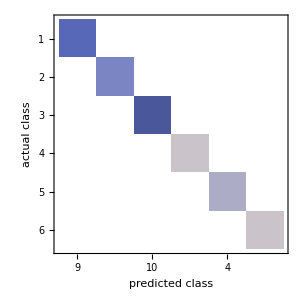

```mathematica
dermaconfusionmatrix=dermacm[best]["ConfusionMatrixPlot"]
```

ClassifierFunctions[] with the available methods and their corresponding accuracies:

```mathematica
SeedRandom[8];
Dataset@ReverseSort@AssociationMap[ClassifierMeasurements[Classify[dermatrain,Method->#,PerformanceGoal->"Quality"],dermatest,"Accuracy"]&,{"NeuralNetwork","RandomForest","NaiveBayes","SupportVectorMachine","NearestNeighbors","LogisticRegression","GradientBoostedTrees","DecisionTree","Markov"}]
```

Dataset[<>]

Training of a FNN for the Dermatology Set:

```mathematica
SeedRandom[8];
netFNN=NetTrain[FNNnetClassification[best,dermadec],dermatrain,LossFunction->dermaLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]];
```

The accuracy of the FNN:

```mathematica
ClassifierMeasurements[netFNN,dermatest]["Accuracy"]
```

0.944444

The resulting Confusion Matrix Plot :

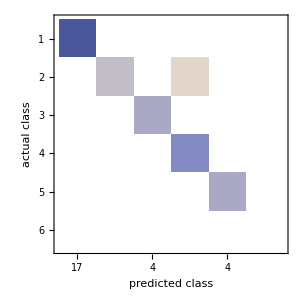

```mathematica
ClassifierMeasurements[netFNN,dermatest]["ConfusionMatrixPlot"]
```

## Mesothelioma

## Description

Data Set Information : Malignant mesotheliomas (MM) are very aggressive tumors of the pleura.These tumors are connected to asbestos exposure, however it may also be related to previous simian virus 40 (SV40) infection and quite possible for genetic predisposition.Molecular mechanisms can also be implicated in the development of mesothelioma.Rural living is associated with the development of mesothelioma.Soil mixtures containing asbestos can be found in Anatolia, Turkey and Greece.
The features are; age, gender, city, asbestos exposure, type of MM, duration of asbestos exposure, diagnosis method, keep 
side, cytology, duration of symptoms, dyspnoea, ache on chest, weakness, habit of cigarette, performance status, White Blood
cell count (WBC), hemoglobin (HGB), platelet count (PLT), sedimentation, blood lactic dehydrogenise (LDH), Alkaline phosphatise 
(ALP), total protein, albumin, glucose, pleural lactic dehydrogenise, pleural protein, pleural albumin, pleural glucose, 
dead or not, pleural effusion, pleural thickness on tomography, pleural level of acidity (pH), C-reactive protein (CRP), class of 
diagnosis.

```mathematica
(*This one has no missing values*)
```

```mathematica
mesoData=ToExpression@Drop[Import["C:/Users/Yury Orlov/Documents/Wolfram Mathematica/Project/Mesothelioma/MesotheliomaData.xlsx",{"Sheets","Data"}],1];

mesoDatawRule=Table[Drop[mesoData⟦i⟧,-1]->Last@mesoData⟦i⟧,{i,1,Length@mesoData}];
mesoDataUnBiased=Join[Select[mesoDatawRule,Values[#]==1&,96],Select[mesoDatawRule,Values[#]==2&]];

{mesotrain,mesotest}={RandomSample[mesoDataUnBiased,Round[0.9Length@mesoDataUnBiased]],Complement[mesoDataUnBiased,mesotrain]};

mesoext=FeatureExtraction[Keys@mesoDataUnBiased,"StandardizedVector"];
{mesotrainSNN,mesotestSNN}={mesoext[Keys@mesotrain]->Values@mesotrain,mesoext[Keys@mesotest]->Values@mesotest};

mesotestSNN=Table[mesotestSNN[[1,i]]->mesotestSNN[[2,i]],{i,1,Length@mesotestSNN⟦1⟧}];
```

```mathematica
mesodec=NetDecoder[{"Class",{1.,2.}}];

mesoLoss=CrossEntropyLossLayer["Index","Target"->NetEncoder[{"Class",{1.,2.}}]];

mesoNet=<|Flatten@Table[{i,j,k}->SNNnetClassification[i,j,k,mesodec],{i,{0.01,0.05,0.1}},{j,{32,64,128,256}},{k,{4,8,16,32}}]|>;

mesoTrainedNet=<|Table[SeedRandom[8];key->NetTrain[mesoNet[key],mesotrainSNN,LossFunction->mesoLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]],{key,Keys@mesoNet}]|>;

mesocm=<|Table[key->ClassifierMeasurements[mesoTrainedNet[key],mesotestSNN],{key,Keys@mesoTrainedNet}]|>;

mesoAccuracy=<|Table[key->mesocm[key]["Accuracy"],{key,Keys@mesoTrainedNet}]|>;
```

```mathematica
Sort[Values@mesoAccuracy]
```

{0.947368,0.947368,0.947368,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
mesoListPlot=ListPlot[mesoAccuracy,PlotTheme->"Detailed",FrameLabel->{"Neural Net","Accuracy"},PlotLabel->Style["Mesothelioma Data",18,Black]]
```

```mathematica
bestmeso=Last@Keys@mesoAccuracy⟦Ordering[Values@mesoAccuracy]⟧(*It goes from worst to the best*)
```

{0.1,256,32}

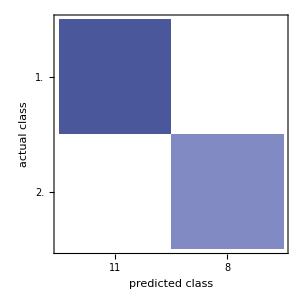

```mathematica
mesoconfusionmatrix=mesocm[bestmeso]["ConfusionMatrixPlot"]
```

```mathematica
Dataset@ReverseSort@AssociationMap[SeedRandom[8];ClassifierMeasurements[Classify[mesotrain,Method->#,PerformanceGoal->"Quality"],mesotest,"Accuracy"]&,{"NeuralNetwork","RandomForest","NaiveBayes","SupportVectorMachine","NearestNeighbors","LogisticRegression","GradientBoostedTrees","DecisionTree","Markov"}]
```

Dataset[<>]

```mathematica
SeedRandom[8];
mesonetFNN=NetTrain[FNNnetClassification[bestmeso,mesodec],mesotrain,LossFunction->mesoLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]];
```

```mathematica
ClassifierMeasurements[mesonetFNN,mesotest]["Accuracy"]
```

0.631579

```mathematica
ClassifierMeasurements[mesonetFNN,mesotest]["ConfusionMatrixPlot"]
```

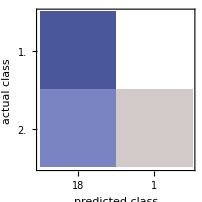
```mathematica
-Graphics-;
```

## Breast Cancer

Importing the dermatology set from UCI Machine Learning repository.  Preprocessing and creation of the train and test sets (for FNN and the ClassifierFunction[]) and the normalized train and test sets (for the SNN)

```mathematica
linkcancer="https://archive.ics.uci.edu/ml/machine-learning-databases/breast-cancer-wisconsin/wdbc.data";

cancerData =Drop[Import[linkcancer, "CSV"],None,1];
cancerData=Drop[SortBy[cancerData,First],145];
cancerDatawRule=Table[Drop[cancerData⟦i⟧,1]->First@cancerData⟦i⟧,{i,1,Length@cancerData}];

{cancertrain,cancertest}={RandomSample[cancerDatawRule,Round[0.9Length@cancerDatawRule]],Complement[cancerDatawRule,cancertrain]};

cancerext=FeatureExtraction[Keys@cancerDatawRule,{"StandardizedVector"}];
{cancertrainSNN,cancertestSNN}={cancerext[Keys@cancertrain]->Values[cancertrain]cancerext[Keys@cancertest]->Values[cancertest]};

cancertestSNN=Table[cancertestSNN[[1,i]]->cancertestSNN[[2,i]],{i,1,Length@cancertestSNN⟦1⟧}];
```

Self-normalizing Neural Network and its training, together with their corresponding Classifier Measurement functions.  48 of SNN are created, with different hyperparameters for each to find the best fit.

```mathematica
cancerdec=NetDecoder[{"Class",{"B","M"}}];

cancerLoss=CrossEntropyLossLayer["Index","Target"->NetEncoder[{"Class",{"B","M"}}]];

cancerNet=<|Flatten@Table[{i,j,k}->SNNnetClassification[i,j,k,cancerdec],{i,{0.01,0.05,0.1}},{j,{32,64,128,256}},{k,{4,8,16,32}}]|>;

cancertrainedNet=<|Table[SeedRandom[8];key->NetTrain[cancerNet[key],cancertrainSNN,LossFunction->cancerLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]],{key,Keys@cancerNet}]|>;

cancercm=<|Table[key->ClassifierMeasurements[cancertrainedNet[key],cancertestSNN],{key,Keys@cancertrainedNet}]|>;

cancerAccuracy=<|Table[key->cancercm[key]["Accuracy"],{key,Keys@cancertrainedNet}]|>;
```

The accuracies for all the 48 SNNs plotted in a ListPlot[]

```mathematica
cancerListPlot=ListPlot[cancerAccuracy,PlotTheme->"Detailed",FrameLabel->{"Neural Net","Accuracy"},PlotLabel->Style["Breast Cancer data",18,Black]]
```

The hyperparameters of  the best (or one of the best)  SNN :

```mathematica
bestcancer=Last@Keys@cancerAccuracy⟦Ordering[Values@cancerAccuracy]⟧
```

{0.1,256,4}

The confusion matrix plot shows the perfect classification of the symptoms :

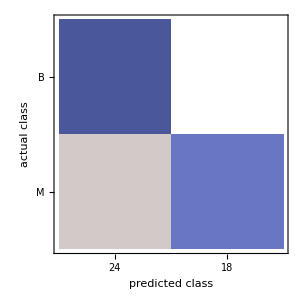

```mathematica
cancerconfusionmatrix=cancercm[bestcancer]["ConfusionMatrixPlot"]
```

```mathematica
Dataset@ReverseSort@AssociationMap[ClassifierMeasurements[Classify[cancertrain,Method->#,PerformanceGoal->"Quality"],cancertest,"Accuracy"]&,{"NeuralNetwork", "RandomForest","NaiveBayes","SupportVectorMachine","NearestNeighbors","LogisticRegression","GradientBoostedTrees","DecisionTree","Markov"}]
```

Dataset[<>]

Training of a FNN:

```mathematica
SeedRandom[8];
cancernetFNN=NetTrain[FNNnetClassification[bestcancer,cancerdec],cancertrain,LossFunction->cancerLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]];
```

The accuracy of the FNN:

```mathematica
ClassifierMeasurements[cancernetFNN,cancertest]["Accuracy"]
```

0.928571

The resulting Confusion Matrix Plot :

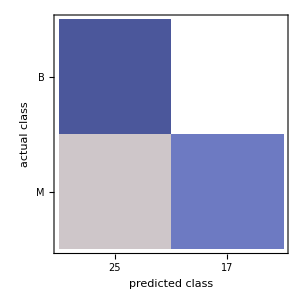

```mathematica
ClassifierMeasurements[cancernetFNN,cancertest]["ConfusionMatrixPlot"]
```

## Parkinson

Importing the dermatology set from UCI Machine Learning repository.  Preprocessing and creation of the train and test sets (for FNN and the ClassifierFunction[]) and the normalized train and test sets (for the SNN)

```mathematica
parkinsonData=Drop[Import["/Users/Liubove/Documents/Wolfram Mathematica/Parkinson/train_data.txt","CSV"],None,1];

parkinsonDatawRule=Table[Drop[parkinsonData⟦i⟧,-1]->Last@parkinsonData⟦i⟧,{i,1,Length@parkinsonData}];


{parkinsontrain,parkinsontest}={RandomSample[parkinsonDatawRule,Round[0.9Length@parkinsonDatawRule]],Complement[parkinsonDatawRule,parkinsontrain]};


parkinsonExt=FeatureExtraction[Keys@parkinsonDatawRule,"StandardizedVector"];

{parkinsontrainSNN,parkinsontestSNN}={parkinsonExt[Keys@parkinsontrain]->Values[parkinsontrain],parkinsonExt[Keys@parkinsontest]->Values[parkinsontest]};

parkinsontestSNN=Table[parkinsontestSNN[[1,i]]->parkinsontestSNN[[2,i]],{i,1,Length@parkinsontestSNN⟦1⟧}];
```

```mathematica
parkinsondec=NetDecoder[{"Class",{0,1}}];

parkinsonLoss=CrossEntropyLossLayer["Index","Target"->NetEncoder[{"Class",{0,1}}]];

parkinsonNet=<|Flatten@Table[{i,j,k}->SNNnetClassification[i,j,k,parkinsondec],{i,{0.01,0.05,0.1}},{j,{32,64,128,256}},{k,{4,8,16,32}}]|>;

parkinsonTrainedNet=<|Table[SeedRandom[8];key->NetTrain[parkinsonNet[key],parkinsontrainSNN,LossFunction->parkinsonLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]],{key,Keys@parkinsonNet}]|>;

parkinsoncm=<|Table[key->ClassifierMeasurements[parkinsonTrainedNet[key],parkinsontestSNN],{key,Keys@parkinsonTrainedNet}]|>;

parkinsonAccuracy=<|Table[key->parkinsoncm[key]["Accuracy"],{key,Keys@parkinsonTrainedNet}]|>;
```

```mathematica
parkiListPlot=ListPlot[parkinsonAccuracy,PlotTheme->"Detailed",FrameLabel->{"Neural Net","Accuracy"},PlotLabel->Style["Parkinson Data",18,Black]]
```

```mathematica
parkibest=Last@Keys@parkinsonAccuracy⟦Ordering[Values@parkinsonAccuracy]⟧
```

{0.05,256,4}

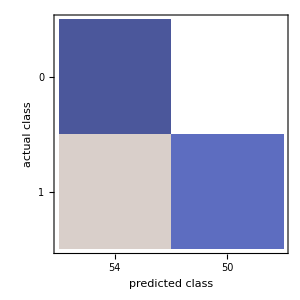

```mathematica
parkiconfusionmatrix=parkinsoncm[parkibest]["ConfusionMatrixPlot"]
```

```mathematica
Dataset@ReverseSort@AssociationMap[ClassifierMeasurements[Classify[parkinsontrain,Method->#,PerformanceGoal->"Quality"],parkinsontest,"Accuracy"]&,{"NeuralNetwork","RandomForest","NaiveBayes","SupportVectorMachine","NearestNeighbors","LogisticRegression","GradientBoostedTrees","DecisionTree","Markov"}]
```

Dataset[<>]

Training of a FNN for the Dermatology Set:

```mathematica
SeedRandom[8];
parkinetFNN=NetTrain[FNNnetClassification[parkibest,parkinsondec],parkinsontrain,LossFunction->parkinsonLoss,MaxTrainingRounds->150,ValidationSet->Scaled[0.1]];
```

The accuracy of the FNN:

```mathematica
ClassifierMeasurements[parkinetFNN,parkinsontest]["Accuracy"]
```

0.980769

The resulting Confusion Matrix Plot :

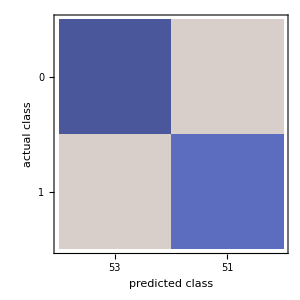

```mathematica
ClassifierMeasurements[parkinetFNN,parkinsontest]["ConfusionMatrixPlot"]
```